# Plotting of Second order Solution family of differential equations.

## Q1. d^2(y)/dx^2 - 6 dy/dx+ 8y=0; y(0) = 1, y’(0) = 1

```mathematica
sol = DSolve[{y''[x]-6*y'[x]+8 y[x]==0, y[0]==1, y'[0]==1},y[x],x]
```

{{y[x]→-1/2 ⅇ^(2 x) (-3+ⅇ^(2 x))}}

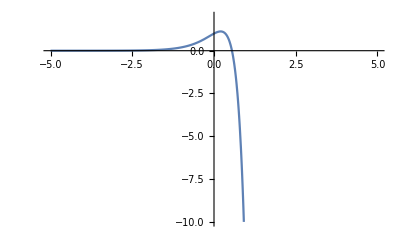

```mathematica
Plot[y[x]/.sol,{x,-5,5},PlotRange->{-10,2}]
```

```mathematica
sol2 = DSolve[y''[x]-6*y'[x]+8 y[x]==0,y[x],x]
```

{{y[x]→ⅇ^(2 x) C[1]+ⅇ^(4 x) C[2]}}

```mathematica
table1 = Table[y[x]/.sol2/.{C[1]->k1,C[2]->k2},{k1,1,3,1},{k2,3,5,1}]
```

{{{ⅇ^(2 x)+3 ⅇ^(4 x)},{ⅇ^(2 x)+4 ⅇ^(4 x)},{ⅇ^(2 x)+5 ⅇ^(4 x)}},{{2 ⅇ^(2 x)+3 ⅇ^(4 x)},{2 ⅇ^(2 x)+4 ⅇ^(4 x)},{2 ⅇ^(2 x)+5 ⅇ^(4 x)}},{{3 ⅇ^(2 x)+3 ⅇ^(4 x)},{3 ⅇ^(2 x)+4 ⅇ^(4 x)},{3 ⅇ^(2 x)+5 ⅇ^(4 x)}}}

```mathematica
Plot[table1,{x,-2,1},PlotRange->{-10,10},PlotTheme->"Marketing"]
```

-Graphics-

## Q2. 2y’’+5y’+3y=0, y[0]=3,y’[0]=-4

```mathematica
sol2 = DSolve[{2 y''[x]+5 y'[x] + 3 y[x] ==0,y[0]==3,y'[0]==-4},y[x],x]
```

{{y[x]→ⅇ^(-3 x/2) (2+ⅇ^(x/2))}}

```mathematica
Plot[y[x]/.sol2,{x,-5,5},PlotTheme->"Marketing"]
```

-Graphics-

## Q3. y’’ + 16 y= 0; y[pi/4]=-3, y’[pi/4]=4

```mathematica
sol3 = DSolve[{y''[x]+16 *y[x]==0,y[pi/4]==-3,y'[pi/4]==4},y[x],x]
```

{{y[x]→(Csc[pi] (-Cos[pi]^2 Cos[4 x]-3 Cos[pi]^2 Cos[4 x] Cot[pi]-3 Cos[pi] Cos[4 x] Sin[pi]-Cos[4 x] Sin[pi]^2-3 Cos[pi]^2 Sin[4 x]+Cos[pi]^2 Cot[pi] Sin[4 x]+Cos[pi] Sin[pi] Sin[4 x]-3 Sin[pi]^2 Sin[4 x]))/((1+Cot[pi]^2) (Cos[pi]^2+Sin[pi]^2))}}

## Q4. y’’ + 100 y= 0,{C[1]=5,10},{C[2]=6,12}

```mathematica
sol4 = DSolve[y''[x]+100*y[x]==0,y[x],x]
```

{{y[x]→C[1] Cos[10 x]+C[2] Sin[10 x]}}

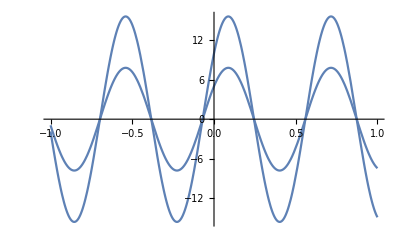

```mathematica
Plot[y[x]/.sol4/.{C[1]->{5,10},C[2]->{6,12}},{x,-1,1}]
```

## Q5. x’’[t] - y[t]=t^2 , y’’[t] +4 x[t] = t; y[0]=1, x[0]=0

```mathematica
sol10=DSolve[{x''[t]-y[t]==t*t,y''[t]+4 x[t]==t,y[0]==1,x[0]==0},{x[t],y[t]},t]
```

{{x[t]→-1/8 ⅇ^-t (2 Cos[t]+2 ⅇ^(2 t) Cos[t]+2 C[2] Cos[t]-2 ⅇ^(2 t) C[2] Cos[t]-C[4] Cos[t]+ⅇ^(2 t) C[4] Cos[t]-4 ⅇ^t Cos[t]^2-2 ⅇ^t t Cos[t]^2+2 Sin[t]-2 ⅇ^(2 t) Sin[t]-2 C[2] Sin[t]-2 ⅇ^(2 t) C[2] Sin[t]-C[4] Sin[t]-ⅇ^(2 t) C[4] Sin[t]-4 ⅇ^t Sin[t]^2-2 ⅇ^t t Sin[t]^2),y[t]→1/4 ⅇ^-t (2 Cos[t]+2 ⅇ^(2 t) Cos[t]-2 C[2] Cos[t]+2 ⅇ^(2 t) C[2] Cos[t]-C[4] Cos[t]+ⅇ^(2 t) C[4] Cos[t]-4 ⅇ^t t^2 Cos[t]^2-2 Sin[t]+2 ⅇ^(2 t) Sin[t]-2 C[2] Sin[t]-2 ⅇ^(2 t) C[2] Sin[t]+C[4] Sin[t]+ⅇ^(2 t) C[4] Sin[t]-4 ⅇ^t t^2 Sin[t]^2)}}

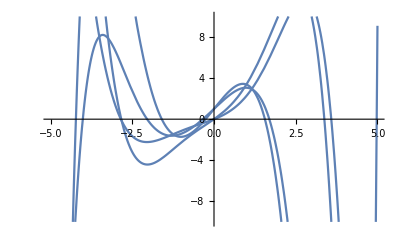

```mathematica
Plot[{x[t],y[t]}/.sol10/.{C[2]->{1,2},C[4]->{3,4}},{t,-5,5},PlotRange->{-10,10}]
```